-Graphics-

Выполнил: Волотовский А., КФ - 37

## Вспомогательный код

```mathematica
Clear["Global`*"];
```

```mathematica
(* Для отладки. *)
trace[value_]:=
(Print[value];
value);
```

```mathematica
(* Построение графиков для ω успело выбесить меня. *)
shutUp=Quiet;
```

### Константы

```mathematica
hQ=Quantity["PlanckConstant"];
kQ=Quantity["BoltzmannConstant"];
cQ=Quantity["SpeedOfLight"];
ℏQ=Quantity["ReducedPlanckConstant"];
```

```mathematica
hN=QuantityMagnitude[UnitConvert[hQ]];
kN=QuantityMagnitude[UnitConvert[kQ]];
cN=QuantityMagnitude[UnitConvert[cQ]];
ℏN=QuantityMagnitude[UnitConvert[ℏQ]];
```

### Формулы

```mathematica
(* Формула Вина (см. 1.4). *)
wienForOmega[T_,ω_,OptionsPattern[{C1->C1,C2->C2}]]:=
OptionValue[C1] ω^3 Exp[-OptionValue[C2] ω/T];
```

```mathematica
(* Формула Рэлея-Джинса (см. 1.5). *)
rayleighJeansForOmega[T_,ω_]:=k T ω^2/(π^2 c^3);
```

```mathematica
(* Формулы Планка (см. 1.6-1.8). *)

(*
    Функции без суффиксов используются для аналитических расчётов,
    Q-функции - для (очень медленного) расчёта с размерностями,
    N-функции для простого и БЫСТРОГО численного расчёта (подходит для построения графиков).
*)
planckForOmega[T_,ω_]:=(ℏ ω^3)/(π^2 c^3)1/(Exp[(ℏ ω)/(k T)]-1);
planckForOmegaQ[T_,ω_]:=(ℏQ ω^3)/(π^2 cQ^3)1/(Exp[(ℏQ ω)/(kQ T)]-1);
planckForOmegaN[T_,ω_]:=(ℏN QuantityMagnitude[ω]^3)/(π^2 cN^3)1/(Exp[(ℏN QuantityMagnitude[ω])/(kN QuantityMagnitude[T])]-1);
planckForLambda[T_,λ_]:=(8π h c)/λ^5 1/(Exp[(h c)/(λ k T)]-1);
planckForLambdaQ[T_,λ_]:=(8π hQ cQ)/λ^5 1/(Exp[(hQ cQ)/(λ kQ T)]-1);
planckForLambdaN[T_,λ_]:=(8π hN cN)/QuantityMagnitude[λ]^5 1/(Exp[(hN cN)/(QuantityMagnitude[λ] kN QuantityMagnitude[ T])]-1);
```

## Задание 1.1

```mathematica
makeLookPravoslavno[expression_]:=
With[{unit=QuantityUnit[expression],magnitude=QuantityMagnitude[expression]},
(* `StringForm` - это костыль, но по-другому у меня вышло. :( *)
StringForm["`1` `2`",magnitude,unit/.{
"Kilograms"->"кг",
"Meters"->"м",
"Seconds"->"с"
}]];
```

## Задание 1.2

-Graphics-

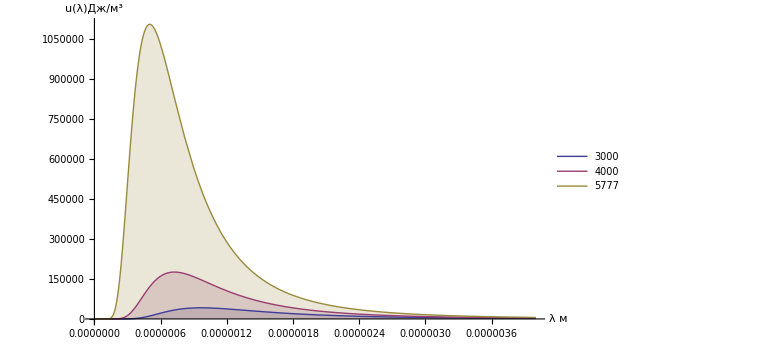

```mathematica
With[{Ts=Map[Quantity[#,"Kelvins"]&,{3000,4000,5777}]},
shutUp @ Plot[Evaluate @ Map[planckForLambdaN[#,Quantity[λ,"Meters"]]&,Ts],{λ,0,4 10^-6},
ImageSize->Large,
Filling->Axis,
PlotRange->All,
PlotLegends->Ts,
AxesLabel->{"λ м",Row[{"u(λ)",("Дж")/("м")^3}," "]}]]
```

```mathematica
With[{Ts=Map[Quantity[#,"Kelvins"]&,{3000,4000,5777}]},
shutUp @ Plot[Evaluate @ Map[planckForOmegaN[#,Quantity[ω,"Meters"]]&,Ts],{ω,0,9 10^15},
ImageSize->Large,
(* `Filling -> Axis` заставляет все графики пропасть :( *)
PlotRange->All,
PlotLegends->Ts,
AxesLabel->{"ω Гц",Row[{"u(ω)",("Дж")/("м")^3}," "]}]]
```

-Graphics-

## Задание 1.3

### ℏ ω << k T

```mathematica
planckForOmega[T,ω]
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^((ω ℏ)/(k T))) π^2)

```mathematica
%/.{ⅇ^x_->ⅇ^χ}
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^χ) π^2)

```mathematica
%/.{ⅇ^χ->Series[Exp[χ],{χ,0,1}]}//Normal
```

(ω^3 ℏ)/(c^3 π^2 χ)

```mathematica
%/.{χ->(ω (ℏ/k))/T}
```

(k T ω^2)/(c^3 π^2)

```mathematica
%==rayleighJeansForOmega[T,ω]
```

True

### ℏ ω >> k T

```mathematica
planckForOmega[T,ω]
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^((ω ℏ)/(k T))) π^2)

```mathematica
(* В области больших частот единичкой в знаменателе можно пренебречь из-за "могучести" экспоненты. *)
%/.{A_/(-1+ⅇ^χ_)->A/ⅇ^χ}
```

(ⅇ^(-(ω ℏ)/(k T)) ω^3 ℏ)/(c^3 π^2)

```mathematica
%==wienForOmega[T,ω,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]
```

True

## Задание 1.4

-Graphics-

```mathematica
(* Такой интеграл не сойдётся из-за ω^2. *)
integralRayleighJeans=shutUp @ Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ rayleighJeansForOmega[T,ω]ⅆω]
```

∫_0^∞ (k T ω^2)/(c^3 π^2)ⅆω

```mathematica
integralWien=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ wienForOmega[T,ω,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]ⅆω]
```

(6 k^4 T^4)/(c^3 π^2 ℏ^3)

```mathematica
makeLookPravoslavno @ N @ UnitConvert[integralWien/.{T->Quantity[2000,"Kelvins"],c->cQ,ℏ->ℏQ,k->kQ}]
```

0.0111844 "\:043a\:0433"/"\:043c"\ "\:0441"^2

```mathematica
integralPlanck=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ planckForOmega[T,ω]ⅆω]
```

(k^4 π^2 T^4)/(15 c^3 ℏ^3)

```mathematica
makeLookPravoslavno @ N @ UnitConvert[integralPlanck/.{T->Quantity[2000,"Kelvins"],c->cQ,ℏ->ℏQ,k->kQ}]
```

0.0121052 "\:043a\:0433"/"\:043c"\ "\:0441"^2

## Задание 1.5

-Graphics-

-Graphics-

```mathematica
integralForPlanck=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ ω planckForOmega[T,ω]ⅆω]
```

(24 k^5 T^5 Zeta[5])/(c^3 π^2 ℏ^4)

```mathematica
makeLookPravoslavno @ N @ UnitConvert[%/.{T->Quantity[2000,"Kelvins"],k->kQ,c->cQ,ℏ->ℏQ}]
```

1.21467×10^13 "\:043a\:0433"/"\:043c"\ "\:0441"^3

## Задание 1.6

-Graphics-

```mathematica
(* См. 1.3 *)
```

```mathematica
(* C1 -> 1/π^2 ℏ / c^3 , C2 ->  ℏ / k *)
```

## Задание 1.7

-Graphics-

```mathematica
With[{f=wienForOmega[T,#,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]&},
Module[{ωLikely,λLikely},
ωLikely=ω/.Solve[D[f[ω],ω]==0,ω,Reals][[2]];
Print @ StringForm["Наиболее вероятная ω: `1` (`2` при T = 2000 К);",ωLikely, makeLookPravoslavno @ N @ UnitConvert[ωLikely/.{T->Quantity[2000,"Kelvins"],k->kQ,ℏ->ℏQ}]];
λLikely=With[{ν=2π ωLikely},c/ν];
Print @ StringForm["Наиболее вероятная λ: `1` (`2` при T = 2000 К).",λLikely,makeLookPravoslavno @ N @ UnitConvert[λLikely/.{T->Quantity[2000,"Kelvins"],c->cQ,k->kQ,ℏ->ℏQ}]];
]]
```

Наиболее вероятная ω: 3\ k\ T/ℏ ("\!\(7.85522×10^14\) \!\(1\/\"\\:0441\"\)" при T = 2000 К);

Наиболее вероятная λ: c\ ℏ/6\ k\ π\ T ("\!\(6.07411×10^-8\) \:043c" при T = 2000 К).

## Вывод

Исходя из закона Планка, я вывел закон Вина (и нашёл константы) и Рэлея-Джинса.
Также я нашёл аналитические выражения для интегральных плотностей вероятностей этих трёх законов.